```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Function2
```

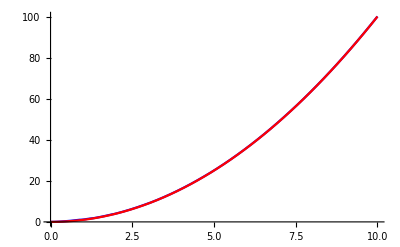

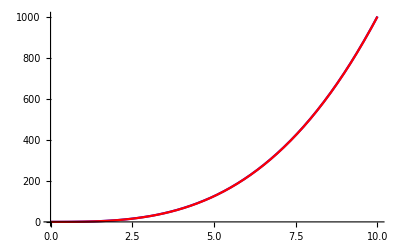

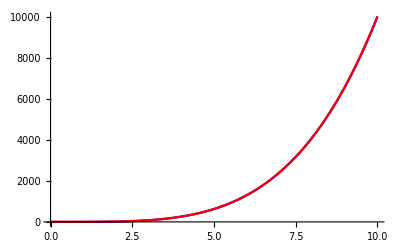

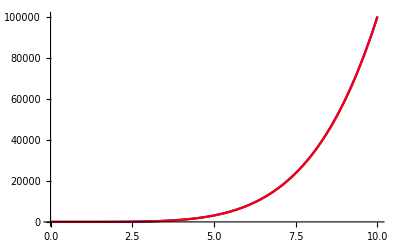

```mathematica
Clear[s1,tf,res0,res1,t0,t1,g0,g1,ge0,ge1,faseportrait]
s1 = NDSolve[{x1'[t]==2*t,x2'[t]==3/2(x1[t] + t^2), x3'[t]==4/3(x2[t] + t* x1[t] + t^3), x4'[t]==5/4(x3[t]+t*x2[t] + t^2*x1[t] +  t^4), x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0},{x1[t],x2[t],x3[t],x4[t]},{t, 0.0,10.0}];
tf = Flatten[Import["t.txt","Data"]];
res0 = Flatten[Import["res0.txt","Data"]];
res1 = Flatten[Import["res1.txt","Data"]];
res2 = Flatten[Import["res2.txt","Data"]];
res3 = Flatten[Import["res3.txt","Data"]];
t0 = Table[{tf[[i]], res0[[i]]},{i,1,Length[tf]}];
t1 =Table[{tf[[i]], res1[[i]]},{i,1,Length[tf]}];
t2 = Table[{tf[[i]], res2[[i]]},{i,1,Length[tf]}];
t3 = Table[{tf[[i]], res3[[i]]},{i,1,Length[tf]}];
g0 = Plot[Interpolation[t0][x],{x,0,10},PlotStyle->Blue];
g1 = Plot[Interpolation[t1][x],{x,0,10},PlotStyle->Blue];
g2 = Plot[Interpolation[t2][x],{x,0,10},PlotStyle->Blue];
g3 =Plot[Interpolation[t3][x],{x,0,10},PlotStyle->Blue];
ge0 = Plot[Evaluate[x1[t]/.s1],{t,0,10},PlotStyle->Red];
ge1 = Plot[Evaluate[x2[t]/.s1],{t,0,10},PlotStyle->Red];
ge2 = Plot[Evaluate[x3[t]/.s1],{t,0,10},PlotStyle->Red];
ge3 = Plot[Evaluate[x4[t]/.s1],{t,0,10},PlotStyle->Red];
Show[g0,ge0, PlotRange->All]
Show[g1,ge1, PlotRange->All]
Show[g2,ge2, PlotRange->All]
Show[g3,ge3, PlotRange->All]
```

```mathematica
Function1 from toolkit
```

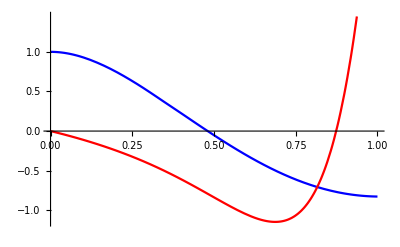

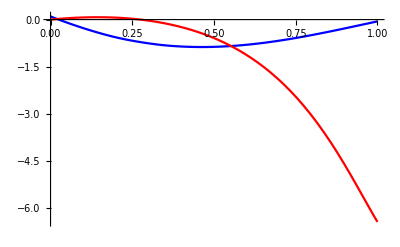

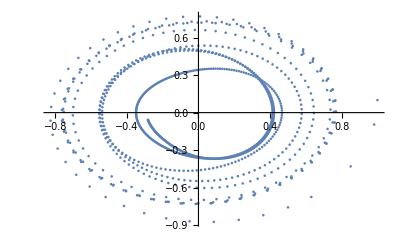

```mathematica
Clear[s1,tf,res0,res1,t0,t1,g0,g1,ge0,ge1,faseportrait]
A = 0.0;
B=1.0;
s1 = NDSolve[{x1'[t]==2x1[t]+ x2[t]^2-1.0,x2'[t]==6x1[t] -x2[t]^2+1.0, x1[0.0]==0,x2[0.0]==0},{x1[t],x2[t]},{t, A,B}];
tf = Flatten[Import["t.txt","Data"]];
res0 = Flatten[Import["res0.txt","Data"]];
res1 = Flatten[Import["res1.txt","Data"]];
t0 = DeleteDuplicates[Table[{tf[[i]], res0[[i]]},{i,1,Length[tf]}]];
t1 = DeleteDuplicates[Table[{tf[[i]], res1[[i]]},{i,1,Length[tf]}]];
faseportrait =  DeleteDuplicates[Table[{res0[[i]], res1[[i]]},{i,1,Length[res0]}]];
g0 = Plot[Interpolation[t0][x],{x,A,B},PlotStyle->Blue];
g1 = Plot[Interpolation[t1][x],{x,A,B},PlotStyle->Blue];
ge0 = Plot[Evaluate[x1[t]/.s1],{t,A,B},PlotStyle->Red];
ge1 = Plot[Evaluate[x2[t]/.s1],{t,A,B},PlotStyle->Red];
Show[g0,ge0, PlotRange->All]
Show[g1,ge1, PlotRange->All]
ListPlot[faseportrait]
```

```mathematica
Function2 from google class
```

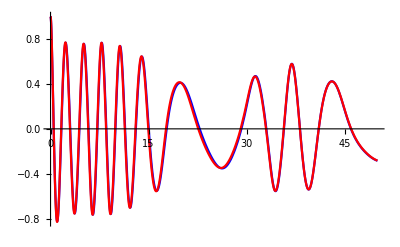

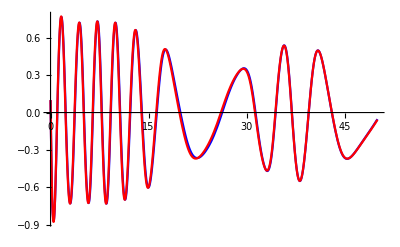

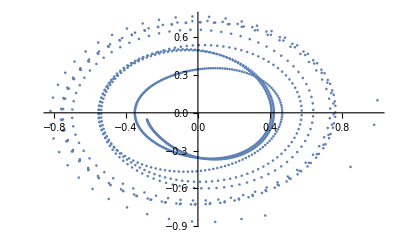

```mathematica
Clear[s1,tf,res0,res1,t0,t1,g0,g1,ge0,ge1, H]
A = 0.0;
B=50.0;
H = (x1[t]^2+x2[t]^2)^2-0.02(x1[t]^2-x2[t]^2);
s1 = NDSolve[{x1'[t]==D[H,x2[t]]-0.1*H*D[H,x1[t]]+0.15*x2[t]*Sin[0.25*t],x2'[t]==-D[H,x1[t]]-0.1*H*D[H,x2[t]]+0.15*x2[t]*Sin[0.25*t], x1[0.0]==1.0,x2[0.0]==0.1},{x1[t],x2[t]},{t, A,B}];
tf = Flatten[Import["t.txt","Data"]];
res0 = Flatten[Import["res0.txt","Data"]];
res1 = Flatten[Import["res1.txt","Data"]];
t0 = DeleteDuplicates[Table[{tf[[i]], res0[[i]]},{i,1,Length[tf]}]];
t1 = DeleteDuplicates[Table[{tf[[i]], res1[[i]]},{i,1,Length[tf]}]];
faseportrait =  DeleteDuplicates[Table[{res0[[i]], res1[[i]]},{i,1,Length[res0]}]];
g0 = Plot[Interpolation[t0][x],{x,A,B},PlotStyle->Blue];
g1 = Plot[Interpolation[t1][x],{x,A,B},PlotStyle->Blue];
ge0 = Plot[Evaluate[x1[t]/.s1],{t,A,B},PlotStyle->Red];
ge1 = Plot[Evaluate[x2[t]/.s1],{t,A,B},PlotStyle->Red];
Show[g0,ge0, PlotRange->All]
Show[g1,ge1, PlotRange->All]
ListPlot[faseportrait]
```

```mathematica
Function3 from toolkit
```

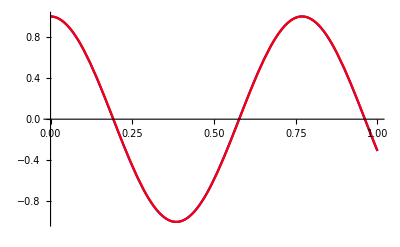

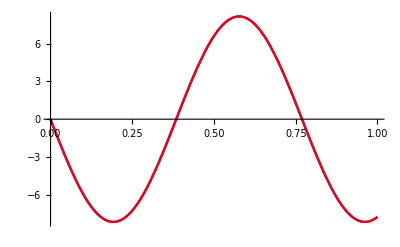

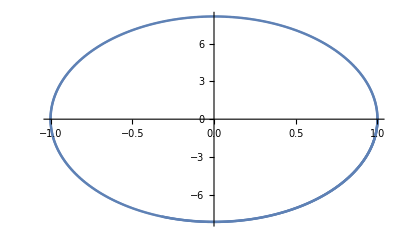

```mathematica
Clear[s1,tf,res0,res1,t0,t1,g0,g1,ge0,ge1, H,k,m]
A = 0.0;k=20.0;
B=1.0;m = 0.3;
s1 = NDSolve[{x1'[t]==x2[t],x2'[t]==-k/m x1[t], x1[0.0]==1.0,x2[0.0]==0.0},{x1[t],x2[t]},{t, A,B}];
tf = Flatten[Import["t.txt","Data"]];
res0 = Flatten[Import["res0.txt","Data"]];
res1 = Flatten[Import["res1.txt","Data"]];
t0 = DeleteDuplicates[Table[{tf[[i]], res0[[i]]},{i,1,Length[tf]}]];
t1 = DeleteDuplicates[Table[{tf[[i]], res1[[i]]},{i,1,Length[tf]}]];
faseportrait =  DeleteDuplicates[Table[{res0[[i]], res1[[i]]},{i,1,Length[res0]}]];
g0 = Plot[Interpolation[t0][x],{x,A,B},PlotStyle->Blue];
g1 = Plot[Interpolation[t1][x],{x,A,B},PlotStyle->Blue];
ge0 = Plot[Evaluate[x1[t]/.s1],{t,A,B},PlotStyle->Red];
ge1 = Plot[Evaluate[x2[t]/.s1],{t,A,B},PlotStyle->Red];
Show[g0,ge0, PlotRange->All]
Show[g1,ge1, PlotRange->All]
ListPlot[faseportrait]
```